Find the embedding of the generating braid into GPA.
See Cain’s printed paper for defining relations.
See Exceptional Quantum Subgroups... graph 8 (blue edges only) for Gamma.

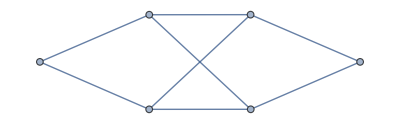

```mathematica
SetDirectory["~/Documents/UNH/Research/code/OTimes/sp4/"];
Clear[GammaAdj, GammaSymb, q, rho,n, dim, lvl, braid];
GammaAdj = { 
{0,1,1,0,0,0},
{1,0,0,1,1,0},
{1,0,0,1,1,0}, 
{0,1,1,0,0,1},
{0,1,1,0,0,1},
{0,0,0,1,1,0} 
};
AdjacencyGraph[ GammaAdj] (* picture of the graph *)
Clear[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo, pp];
SetNonCommutative[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo, pp];
GammaSymb = { 
{0,aa,bb,0,0,0},
{cc,0,0,dd,ee,0},
{ff,0,0,gg,hh,0}, 
{0,ii,jj,0,0,kk},
{0,ll,mm,0,0,nn},
{0,0,0,oo,pp,0}
};
quan[n_, qew_]:=(qew^n-qew^-n)/(qew-qew^-1);
inDeg[z_]:=360(z//Arg)/(2Pi)//N
dim=2;
lvl = 3;
q=Exp[(2Pi I)/(4(dim+lvl+1))];
rho = q^5; (* should this be -q^5??? *)
```

```mathematica
Hom0to2 = GetHomBasisList[GammaSymb, 0,2];
Hom0to0 = GetHomBasisList[GammaSymb,0,0];
Hom1to1 = GetHomBasisList[GammaSymb,1,1];
Hom2to4 = GetHomBasisList[GammaSymb, 2,4];
Hom2to3 = GetHomBasisList[GammaSymb, 2,3];
Hom2to2 = GetHomBasisList[GammaSymb,2,2];
Hom2to1 = GetHomBasisList[GammaSymb,2,1];
Hom2to0 = GetHomBasisList[GammaSymb,2,0];
Hom1to2 = GetHomBasisList[GammaSymb,1,2];
Hom1to1 = GetHomBasisList[GammaSymb,1,1];
Hom1to0 = GetHomBasisList[GammaSymb,1,0];
Hom0to1 = GetHomBasisList[GammaSymb,0,1];
Hom0to0 = GetHomBasisList[GammaSymb,0,0];
Hom0to2 = GetHomBasisList[GammaSymb, 0,2];
Hom3to3 = GetHomBasisList[GammaSymb, 3,3];
Cap = GenerateCap[GammaAdj, GammaSymb];
Cup = InTermsOf[Dagger[Cap], Hom0to2];
Cup = ScaleByConstant[Cup, -1];
Stick = GenerateStick[GammaAdj, GammaSymb];
DoubleStick = InTermsOf[BigTens[Stick, Stick], Hom2to2];

BubbleLHS = InTermsOf[BigCompose[Cup, Cap],Hom0to0];
BubbleLHS//GPAFullSimplify

InTermsOf[Comp[{Tens[{Stick, Cup}],Tens[{Cap, Stick}]}], Hom1to1]
InTermsOf[Comp[{Tens[{Cup, Stick}],Tens[{Stick, Cap}]}], Hom1to1]
```

{<|scalar→-1-√3,p→1,q→1,s→1,t→1|>,<|scalar→-1-√3,p→2,q→2,s→2,t→2|>,<|scalar→-1-√3,p→3,q→3,s→3,t→3|>,<|scalar→-1-√3,p→4,q→4,s→4,t→4|>,<|scalar→-1-√3,p→5,q→5,s→5,t→5|>,<|scalar→-1-√3,p→6,q→6,s→6,t→6|>}

{<|scalar→1,p→aa,q→aa,s→1,t→2|>,<|scalar→1,p→bb,q→bb,s→1,t→3|>,<|scalar→1,p→cc,q→cc,s→2,t→1|>,<|scalar→1,p→dd,q→dd,s→2,t→4|>,<|scalar→1,p→ee,q→ee,s→2,t→5|>,<|scalar→1,p→ff,q→ff,s→3,t→1|>,<|scalar→1,p→gg,q→gg,s→3,t→4|>,<|scalar→1,p→hh,q→hh,s→3,t→5|>,<|scalar→1,p→ii,q→ii,s→4,t→2|>,<|scalar→1,p→jj,q→jj,s→4,t→3|>,<|scalar→1,p→kk,q→kk,s→4,t→6|>,<|scalar→1,p→ll,q→ll,s→5,t→2|>,<|scalar→1,p→mm,q→mm,s→5,t→3|>,<|scalar→1,p→nn,q→nn,s→5,t→6|>,<|scalar→1,p→oo,q→oo,s→6,t→4|>,<|scalar→1,p→pp,q→pp,s→6,t→5|>}

{<|scalar→1,p→aa,q→aa,s→1,t→2|>,<|scalar→1,p→bb,q→bb,s→1,t→3|>,<|scalar→1,p→cc,q→cc,s→2,t→1|>,<|scalar→1,p→dd,q→dd,s→2,t→4|>,<|scalar→1,p→ee,q→ee,s→2,t→5|>,<|scalar→1,p→ff,q→ff,s→3,t→1|>,<|scalar→1,p→gg,q→gg,s→3,t→4|>,<|scalar→1,p→hh,q→hh,s→3,t→5|>,<|scalar→1,p→ii,q→ii,s→4,t→2|>,<|scalar→1,p→jj,q→jj,s→4,t→3|>,<|scalar→1,p→kk,q→kk,s→4,t→6|>,<|scalar→1,p→ll,q→ll,s→5,t→2|>,<|scalar→1,p→mm,q→mm,s→5,t→3|>,<|scalar→1,p→nn,q→nn,s→5,t→6|>,<|scalar→1,p→oo,q→oo,s→6,t→4|>,<|scalar→1,p→pp,q→pp,s→6,t→5|>}

The above means we have good skein theory: δ < 0, and zig-zag has a coefficient of 1.
Now we can go about actually finding the braid.

```mathematica
aVar=Table[Symbol["a"<>ToString[i]],{i,1,dim2to2}];
braidSym = Hom2to2;
For[i=1,i<=dim2to2,i++,
braidSym[[i]][["scalar"]] = aVar[[i]]
];

(*Clear[xVar, Ps];
xVar=Table[Symbol["x"<>ToString[i]],{i,1,dim2to2}];
Ps = Hom2to2;
For[i=1,i<=dim2to2,i++,
Ps[[i]][["scalar"]] = xVar[[i]]
];*)
```

Define inverse of the braid.

```mathematica
L1 = InTermsOf[BigTens[Cup, DoubleStick], Hom2to4]//FullSimplify;
L2 = Tens[{Stick, braidSym, Stick}]//CombineLikeTerms;
L3 = BigTens[DoubleStick, Cap]//CombineLikeTerms//FullSimplify;
braidInvSym = Comp[{L1,L2,L3}];
braidInvSym = InTermsOf[braidInvSym, Hom2to2]//GPAFullSimplify;
```

Inverse of the inverse of the braid...

```mathematica
L1 = InTermsOf[BigTens[Cup, DoubleStick], Hom2to4]//FullSimplify;
L2 = Tens[{Stick, braidInvSym, Stick}]//CombineLikeTerms;
L3 = BigTens[DoubleStick, Cap]//CombineLikeTerms//FullSimplify;
braidInvInvSym = Comp[{L1,L2,L3}];
braidInvInvSym = InTermsOf[braidInvInvSym, Hom2to2]//GPAFullSimplify;
```

```mathematica
invinvEqns = GetEqns[braidSym,braidInvInvSym];
invinvSol = (invinvEqns//Solve)[[1]];
```

Imposing invinvSol from here on, implicitly.

```mathematica
braidSym = braidSym/.invinvSol;
```

Twist equations

```mathematica
twistLHS = Comp[{
BigTens[Stick, Cup],
BigTens[braidSym, Stick],
BigTens[Stick, Cap]
}];
twistLHS = InTermsOf[twistLHS, Hom1to1]//GPAFullSimplify;

twistRHS = ScaleByConstant[Stick, rho^-1];
twistEqns1 = GetEqns[twistLHS, twistRHS]//FullSimplify;

twistInvLHS = Comp[{
BigTens[Stick, Cup],
BigTens[braidInvSym, Stick],
BigTens[Stick, Cap]
}];
twistInvLHS = InTermsOf[twistInvLHS, Hom1to1]//GPAFullSimplify;
twistInvRHS = ScaleByConstant[Stick, rho^1];
twistEqns2 = GetEqns[twistInvLHS, twistInvRHS];

twistEqns = Join[twistEqns1, twistEqns2]//FullSimplify;
```

overUnder: relation between braid and inverse braid.

```mathematica
q-q^-1//FullSimplify
```

Root0.518 ⅈRoot[1+4 #1^2+#1^4&,4]0.

```mathematica
overUnderLHS = Add[braidSym, ScaleByConstant[braidInvSym,-1]];

overUnderRHS1 = DoubleStick;

overUnderRHS2 = BigCompose[Cap, Cup];
overUnderRHS2 = InTermsOf[overUnderRHS2, Hom2to2]//GPAFullSimplify;
overUnderRHS2 = ScaleByConstant[overUnderRHS2, -1];

overUnderRHS = Add[overUnderRHS1, overUnderRHS2]//GPAFullSimplify;
overUnderRHS = ScaleByConstant[overUnderRHS, Root"0.518" ⅈRoot[1+4 #1^2+#1^4&,4]0.]//GPAFullSimplify;

overUnderEqns = GetEqns[overUnderLHS, overUnderRHS]//FullSimplify;
```

```mathematica
linearEqns = Join[twistEqns, overUnderEqns];
linearEqns = Parallelize[ Map[FullSimplify, linearEqns] ];
```

```mathematica
linearSol = (Join[twistEqns,overUnderEqns]//FullSimplify//Solve)[[1]]//FullSimplify;
```

Solve::ztest: Unable to decide whether numeric quantities {√(-1+√3)+√(1/2 (1+√3))-√(3/2 (1+√3)),2 √(-1+√3)+2 √(3 (-1+√3))-2 √(2 (1+√3)),«8»,«11»} are equal to zero. Assuming they are.

Get Reid2Eqns

```mathematica
Reid2LHS = InTermsOf[BigCompose[braidSym, braidInvSym], Hom2to2]//FullSimplify;
Reid2Eqns = GetEqns[Reid2LHS, DoubleStick]/.linearSol;
Reid2Eqns = Parallelize[ Map[FullSimplify, Reid2Eqns]];
```

```mathematica
Reid2Sol = (Parallelize[
Map[FullSimplify,Reid2Eqns/.{a15->ⅈ √(-5+3 √3)-a14,a46->a14,a97->ⅈ √(-5+3 √3)-a14, a94->a14}/.a14->1/2 (-√(3-√3)+ⅈ √(-5+3 √3))/.a30->Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074]
]//Solve//FullSimplify)[[1]];
```

```mathematica
Reid2Sol
```

{a10→1/(2 a11),a102→-a106/(√2 a42),a103→-a42/(√2 a106),a107→1/(2 a106),a25→-(√(1/2 (-1+√3)) a42)/a11,a29→1/(2 a42),a58→a11/(√2 a42)}

{a10→1/(2 a11),a102→-a106/(√2 a42),a103→-a42/(√2 a106),a107→1/(2 a106),a25→-(√(1/2 (-1+√3)) a42)/a11,a29→1/(2 a42),a58→a11/(√2 a42)}

Get Reid3Eqns

```mathematica
LHS1 = BigTens[Stick, braidInvSym]//CombineLikeTerms//GPAFullSimplify;
LHS2 = BigTens[braidSym, Stick]//CombineLikeTerms//GPAFullSimplify;
LHS3 = BigTens[Stick, braidSym]//CombineLikeTerms//GPAFullSimplify;
reidLeft = Comp[{LHS1, LHS2, LHS3}]//CombineLikeTerms//GPAFullSimplify;
reidLeft = InTermsOf[reidLeft, Hom3to3]//GPAFullSimplify;

RHS1 = BigTens[braidSym, Stick]//CombineLikeTerms//GPAFullSimplify;
RHS2 = BigTens[Stick, braidSym]//CombineLikeTerms//GPAFullSimplify;
RHS3 = BigTens[braidInvSym, Stick]//CombineLikeTerms//GPAFullSimplify;
reidRight = Comp[{RHS1, RHS2, RHS3}]//CombineLikeTerms//GPAFullSimplify;
reidRight = InTermsOf[reidRight, Hom3to3]//GPAFullSimplify;

Reid3Eqns = GetEqns[reidLeft, reidRight];
```

```mathematica
Now[]
Reid3Eqns = Parallelize[ Map[RootReduce, Reid3Eqns/.linearSol/.{a15->ⅈ √(-5+3 √3)-a14,a46->a14,a97->ⅈ √(-5+3 √3)-a14, a94->a14}/.a14->1/2 (-√(3-√3)+ⅈ √(-5+3 √3))/.a30->Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074/.Reid2Sol]];
Now[]
Reid3Eqns = Parallelize[ Map[FullSimplify, Reid3Eqns]]//DeleteDuplicates
Now[]
```

Thu 20 Mar 2025 08:49:44GMT-4[]

Thu 20 Mar 2025 08:49:45GMT-4[]

{True}

Thu 20 Mar 2025 08:55:45GMT-4[]

```mathematica
Reid3Eqns//TableForm
```

True

```mathematica
braidSol = aVar/.linearSol/.{a15->ⅈ √(-5+3 √3)-a14,a46->a14,a97->ⅈ √(-5+3 √3)-a14, a94->a14}/.a14->1/2 (-√(3-√3)+ⅈ √(-5+3 √3))/.a30->Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074/.Reid2Sol/.a11->quan[3,q]/.a42->quan[2,q]/.a106->quan[2,q]//FullSimplify;
```

```mathematica
a42/(√2 a11)/.a11->quan[3,q]/.a42->quan[2,q]//FullSimplify
```

1/2

```mathematica
-(√(-1+√3))/(2 a106)/.a106->quan[2,q]//FullSimplify
```

-1/2 √(-5+3 √3)

```mathematica
quan[2,q]//FullSimplify
```

√(2+√3)

```mathematica
{Range[112],braidSol, braidSol//N//Abs, braidSol//inDeg}//Transpose//MatrixForm
```

(1 | Root-0.354+0.612 ⅈRoot[1+2 #1^2+4 #1^4&,2]-0.3535533905932738 | 0.707107 | 120.
2 | Root0.612+0.354 ⅈRoot[1-2 #1^2+4 #1^4&,4]0.6123724356957945 | 0.707107 | 30.
3 | Root0.612+0.354 ⅈRoot[1-2 #1^2+4 #1^4&,4]0.6123724356957945 | 0.707107 | 30.
4 | Root-0.354+0.612 ⅈRoot[1+2 #1^2+4 #1^4&,2]-0.3535533905932738 | 0.707107 | 120.
5 | 1/2 (3^(1/4)+Root0.518 ⅈRoot[1+4 #1^2+#1^4&,4]0.) | 0.707107 | 21.4707
6 | 1/2 | 0.5 | 0.
7 | 1 | 1. | 0.
8 | 1/4 ⅈ (-√2+2 ⅈ 3^(1/4)+√6) | 0.707107 | 158.529
9 | 1/4 ⅈ (-√2+2 ⅈ 3^(1/4)+√6) | 0.707107 | 158.529
10 | 1/4 (-1+√3) | 0.183013 | 0.
11 | 1+√3 | 2.73205 | 0.
12 | 1/2 (3^(1/4)+Root0.518 ⅈRoot[1+4 #1^2+#1^4&,4]0.) | 0.707107 | 21.4707
13 | (-1)^(5/12)+Root-0.518 ⅈRoot[1+4 #1^2+#1^4&,3]0. | 0.517638 | 60.
14 | Root-0.563+0.221 ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472 | 0.605 | 158.529
15 | Root0.563+0.221 ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472 | 0.605 | 21.4707
16 | Root-0.563+0.221 ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472 | 0.605 | 158.529
17 | Root0.482+0.518 ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,8]0.48171652200114257 | 0.707107 | 47.0586
18 | Root0.259+0.259 ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074 | 0.366025 | 45.
19 | Root0.563+0.221 ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472 | 0.605 | 21.4707
20 | Root0.259+0.259 ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074 | 0.366025 | 45.
21 | Root-0.482+0.518 ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,2]-0.48171652200114257 | 0.707107 | 132.941
22 | Root-0.448+0.259 ⅈRoot[1-4 #1^2+15 #1^4-4 #1^6+#1^8&,4]-0.4482877360840268 | 0.517638 | 150.
23 | -√(-1+√3) | 0.8556 | 180.
24 | -√(2 (1+√3)) | 2.33754 | 180.
25 | -1/2 √(-1+√3) | 0.4278 | 180.
26 | Root-0.259+0.259 ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074 | 0.366025 | 135.
27 | √(2+√3) | 1.93185 | 0.
28 | Root-0.157Root[-1+40 #1^2+32 #1^4&,1]-0.15658560865650772 | 0.156586 | 180.
29 | (√(2-√3))/2 | 0.258819 | 0.
30 | Root-0.259+0.259 ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074 | 0.366025 | 135.
31 | Root-0.658+0.259 ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,2]-0.6580370064762462 | 0.707107 | 158.529
32 | -1/(√2) | 0.707107 | 180.
33 | -1/(√2) | 0.707107 | 180.
34 | 1/4 (-ⅈ √2+2 3^(1/4)+ⅈ √6) | 0.707107 | 21.4707
35 | Root-0.448+0.259 ⅈRoot[1-4 #1^2+15 #1^4-4 #1^6+#1^8&,4]-0.4482877360840268 | 0.517638 | 150.
36 | -1/2 √(-1+√3) | 0.4278 | 180.
37 | Root-0.157Root[-1+40 #1^2+32 #1^4&,1]-0.15658560865650772 | 0.156586 | 180.
38 | -√(-1+√3) | 0.8556 | 180.
39 | Root-0.259+0.259 ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074 | 0.366025 | 135.
40 | (√(2-√3))/2 | 0.258819 | 0.
41 | -√(2 (1+√3)) | 2.33754 | 180.
42 | √(2+√3) | 1.93185 | 0.
43 | Root-0.259+0.259 ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074 | 0.366025 | 135.
44 | (-1)^(5/12)+Root-0.518 ⅈRoot[1+4 #1^2+#1^4&,3]0. | 0.517638 | 60.
45 | Root0.563+0.221 ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472 | 0.605 | 21.4707
46 | Root-0.563+0.221 ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472 | 0.605 | 158.529
47 | Root0.563+0.221 ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472 | 0.605 | 21.4707
48 | Root-0.482+0.518 ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,2]-0.48171652200114257 | 0.707107 | 132.941
49 | Root0.259+0.259 ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074 | 0.366025 | 45.
50 | Root-0.563+0.221 ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472 | 0.605 | 158.529
51 | Root0.259+0.259 ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074 | 0.366025 | 45.
52 | Root0.482+0.518 ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,8]0.48171652200114257 | 0.707107 | 47.0586
53 | Root0.658+0.259 ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,8]0.6580370064762462 | 0.707107 | 21.4707
54 | (√(2-√3))/2 | 0.258819 | 0.
55 | √(2+√3) | 1.93185 | 0.
56 | 1/4 ⅈ (-√2+2 ⅈ 3^(1/4)+√6) | 0.707107 | 158.529
57 | 1/4 (-ⅈ √2+2 3^(1/4)+ⅈ √6) | 0.707107 | 21.4707
58 | 1 | 1. | 0.
59 | 1/2 | 0.5 | 0.
60 | 1/4 ⅈ (-√2+2 ⅈ 3^(1/4)+√6) | 0.707107 | 158.529
61 | Root-0.482+0.518 ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,2]-0.48171652200114257 | 0.707107 | 132.941
62 | Root0.259+0.259 ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074 | 0.366025 | 45.
63 | Root0.563+0.221 ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472 | 0.605 | 21.4707
64 | Root0.259+0.259 ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074 | 0.366025 | 45.
65 | Root0.482+0.518 ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,8]0.48171652200114257 | 0.707107 | 47.0586
66 | Root-0.563+0.221 ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472 | 0.605 | 158.529
67 | Root0.563+0.221 ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472 | 0.605 | 21.4707
68 | Root-0.563+0.221 ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472 | 0.605 | 158.529
69 | (-1)^(5/12)+Root-0.518 ⅈRoot[1+4 #1^2+#1^4&,3]0. | 0.517638 | 60.
70 | Root-0.259+0.259 ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074 | 0.366025 | 135.
71 | 1/4 (√2-√6) | 0.258819 | 180.
72 | √(1/2 (-1+√3)) | 0.605 | 0.
73 | -√(2+√3) | 1.93185 | 180.
74 | Root-0.259+0.259 ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074 | 0.366025 | 135.
75 | -√(1+√3) | 1.65289 | 180.
76 | √(1/2 (-1+√3)) | 0.605 | 0.
77 | -1/2 √(-5+3 √3) | 0.221445 | 180.
78 | Root-0.448+0.259 ⅈRoot[1-4 #1^2+15 #1^4-4 #1^6+#1^8&,4]-0.4482877360840268 | 0.517638 | 150.
79 | 1/2 (-3^(1/4)+Root0.518 ⅈRoot[1+4 #1^2+#1^4&,4]0.) | 0.707107 | 158.529
80 | 1+√3 | 2.73205 | 0.
81 | 1/4 (-1+√3) | 0.183013 | 0.
82 | 1/4 (-ⅈ √2+2 3^(1/4)+ⅈ √6) | 0.707107 | 21.4707
83 | Root-0.259+0.259 ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074 | 0.366025 | 135.
84 | -√(2+√3) | 1.93185 | 180.
85 | √(1/2 (-1+√3)) | 0.605 | 0.
86 | 1/4 (√2-√6) | 0.258819 | 180.
87 | Root-0.259+0.259 ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074 | 0.366025 | 135.
88 | -1/2 √(-5+3 √3) | 0.221445 | 180.
89 | √(1/2 (-1+√3)) | 0.605 | 0.
90 | -√(1+√3) | 1.65289 | 180.
91 | ((1/2+ⅈ/2) ((-2+ⅈ)+√3))/(√2) | 0.517638 | 150.
92 | Root0.482+0.518 ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,8]0.48171652200114257 | 0.707107 | 47.0586
93 | Root0.259+0.259 ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074 | 0.366025 | 45.
94 | Root-0.563+0.221 ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472 | 0.605 | 158.529
95 | Root0.259+0.259 ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074 | 0.366025 | 45.
96 | Root-0.482+0.518 ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,2]-0.48171652200114257 | 0.707107 | 132.941
97 | Root0.563+0.221 ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472 | 0.605 | 21.4707
98 | Root-0.563+0.221 ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472 | 0.605 | 158.529
99 | Root0.563+0.221 ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472 | 0.605 | 21.4707
100 | (-1)^(5/12)+Root-0.518 ⅈRoot[1+4 #1^2+#1^4&,3]0. | 0.517638 | 60.
101 | 1/4 ⅈ (-√2+2 ⅈ 3^(1/4)+√6) | 0.707107 | 158.529
102 | -1/(√2) | 0.707107 | 180.
103 | -1/(√2) | 0.707107 | 180.
104 | 1/2 (3^(1/4)+Root0.518 ⅈRoot[1+4 #1^2+#1^4&,4]0.) | 0.707107 | 21.4707
105 | 1/2 (3^(1/4)+Root0.518 ⅈRoot[1+4 #1^2+#1^4&,4]0.) | 0.707107 | 21.4707
106 | √(2+√3) | 1.93185 | 0.
107 | (√(2-√3))/2 | 0.258819 | 0.
108 | 1/2 (-3^(1/4)+Root0.518 ⅈRoot[1+4 #1^2+#1^4&,4]0.) | 0.707107 | 158.529
109 | Root-0.354+0.612 ⅈRoot[1+2 #1^2+4 #1^4&,2]-0.3535533905932738 | 0.707107 | 120.
110 | Root0.612+0.354 ⅈRoot[1-2 #1^2+4 #1^4&,4]0.6123724356957945 | 0.707107 | 30.
111 | Root0.612+0.354 ⅈRoot[1-2 #1^2+4 #1^4&,4]0.6123724356957945 | 0.707107 | 30.
112 | Root-0.354+0.612 ⅈRoot[1+2 #1^2+4 #1^4&,2]-0.3535533905932738 | 0.707107 | 120.)

```mathematica
Table[1/Sqrt[quan[ind,q]]//N//Chop,{ind,1,11}]//TableForm
```

1.
0.719471
0.605
0.54668
0.517638
0.508743
0.517638
0.54668
0.605
0.719471
1.

```mathematica
1/Sqrt[quan[3,q]]//FullSimplify
1/Sqrt[quan[3,q]]//N//Chop
```

1/(√(1+√3))

0.605